### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/16

### Keywords

Details

# Model 1.6-1.7

Model 1.6 and 1.7 are the models for study the parasite population dynamics and fever in an infected patient. There were proposed by Dominic Kwiatkowski and Martin Nowak (Kwiatkowski, D. & Nowak, M. (1991) Periodic and chaotic host-parasite interactions in human malaria Proceedings of the National Academy of Sciences of the United States of America 88, 5111-5113).

## Model 1.6

Model 1.6 is the model for the population dynamics of young parasites (x(t), 0-24 hours) and old parasites (y(t), 24-48 hours).  See the equation 1. Here f(x_t) = e^(-p x(t)) and g(x_t) = e^(-s x(t)).

-Graphics-

The function F related with the body temperature of the patient is written as F(x) = 36.5+4 (1-e^(-0.0003 x(t))).

model | the model ID
initxy | the initial number of x(0) and y(0). # {x,y}
initd | the values of d_1 and d_2. #{d1,d2}
r | model constant (see equation 1)
ps | the values of p and s for f(x_t) = e^(-p x(t)) and g(x_t) = e^(-s x(t))
runsteps | the model run steps
outform | the output form. (model 1.6 has only one output form (0))

List of the model 1.6 parameters .

Examples of model 1.6 outputs

```mathematica
lsout=IDVL["mod1_6.in"];
```

******INDIVARIA*****

model: 1.6

outform: 0

********************

model: 1.6

initxy: {1,1}

initd: {1,1}

r: 4.

ps: {0.00001,0.001}

runsteps: 50

outform: 0

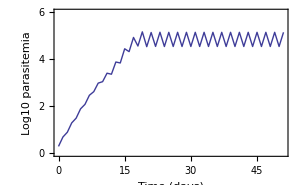

```mathematica
ls=Table[{lsout[[i,1]],Log10@lsout[[i,4]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6},Frame->{True,True,False,False},FrameLabel->{"Time (days)","Log10 parasitemia"}]
```

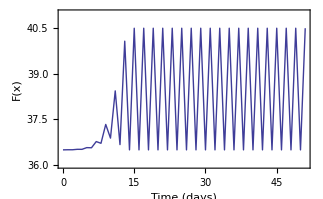

```mathematica
ls=Table[{lsout[[i,1]],lsout[[i,5]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{36,41},Frame->{True,True,False,False},FrameLabel->{"Time (days)","F(x)"}]
```

## Model 1.7

Model 1.7 is another version of model 1.6. It is from Kwiatkowski, D. & Nowak, M. (1991) Periodic and chaotic host-parasite interactions in human malaria Proceedings of the National Academy of Sciences of the United States of America 88, 5111-5113. The parasite population in this model is now divided into four stages of development: x1 (0-12 hours posinvation), x2 (12-24 hours posinvation), x3 (24-36 posinvation) and x4 (36-48 hours posinvation). So the equation 1 (see model 1.6 above) is now changed to

x1(t+0.5) = (1 - h)*r*d4*x4(t)*f4 + h*d1*x1(t)*f1;
    x2(t+0.5) = (1 - h)*d1*x1(t)*f1 + h*d2*x2(t)*f2;
    x3(t+0.5) = (1 - h)*d2*x2(t)*f2 + h*d3*x3(t)*f3;
    x4(t+0.5) = (1 - h)*d3*x3(t)*f3 + h*d4*x4(t)*f4;

where f1 = Exp[-s1*x1], f2 = Exp[-s2*x1], f3 = Exp[-s3*x1] and  f4 = Exp[-s4*x1].

The output of model 1.7 is the list of x1,x2,x3, x4 and F(x1) over time. F(x1) is the function related with the body temperature, F(x1) = 36.5+4 (1-e^(-0.0003 x1(t))).

model | the model ID
initx | the initial number of x1,x2,x3,x4. # {x1,x2,x3,x4}
initd | the values of d1,d2,d3,d4. #{d1,d2,d3,d4}
r | model constant 
h | model time step (shoud be 0.5)
inits | the values of s1,s2,s3,s4 #{s1,s2,s3,s4}
runsteps | the model run steps
outform | the output form. (model 1.7 has only one output form (0))

List of the model 1.7 parameters .

Examples of model 1.7 outputs

```mathematica
lsout=IDVL["mod1_7.in"];
```

******INDIVARIA*****

model: 1.7

outform: 0

********************

model: 1.7

initx: {1,1,1,1}

r: 16

h: 0.05

initd: {1,1,1,1}

inits: {0.00001,0.00002,0.0001,0.001}

runsteps: 50

outform: 0

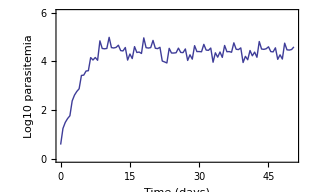

```mathematica
ls=Table[{lsout[[i,1]],Log10@lsout[[i,3]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6},Frame->{True,True,False,False},FrameLabel->{"Time (days)","Log10 parasitemia"}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses